# Graph theory, NP hard combinatorial optimization and world geography

Author Name

Abstract

## Section

I can find a graph of all countries in Eurasia

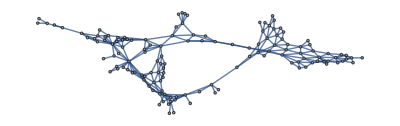

```mathematica
ℰ=NestGraph[CountryData[#,"BorderingCountries"]&,Entity["Country","France"],12];
ℰ=UndirectedGraph[ℰ,ImageSize->Full,VertexLabels->(Normal@AssociationMap[Placed[Labeled[#["FlagImage"],#["Name"]],Tooltip]&,VertexList[ℰ]])]
```

Analyze the structure of the graph. What countries are farthest away and how far are they?

```mathematica
mostDistantCountries=GraphPeriphery[ℰ]
```

{East Timor,Papua New Guinea,Lesotho}

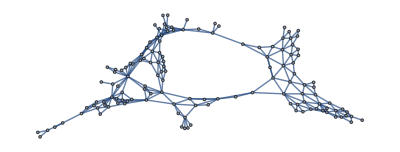

```mathematica
𝒥=NestGraph[CountryData[#,"BorderingCountries"]&,Entity["Country","Jordan"],9];
𝒥=UndirectedGraph[𝒥,ImageSize->Full,VertexLabels->(Normal@AssociationMap[Placed[Labeled[#["FlagImage"],#["Name"]],Tooltip]&,VertexList[𝒥]])]
```

```mathematica
AssociationMap[GraphPeriphery[𝒥,Method->#]&,{"Dijkstra","FloydWarshall","Johnson","PseudoDiameter"}]
```

<|Dijkstra→{East Timor,Papua New Guinea,Lesotho},FloydWarshall→{East Timor,Papua New Guinea,Lesotho},Johnson→{East Timor,Papua New Guinea,Lesotho},PseudoDiameter→{}|>

```mathematica
GraphCenter[ℰ]
```

{Syria,Jordan}

```mathematica
GraphCenter[𝒥]
```

{}

```mathematica
Map[GraphPeriphery[#]&,{ℰ,𝒥}]
```

{{East Timor,Papua New Guinea,Lesotho},{}}

```mathematica
Map[GraphRadius[#]&,{ℰ,𝒥}]
```

{9,∞}

```mathematica
Map[GraphDiameter[#]&,{ℰ,𝒥}]
```

{18,∞}

```mathematica
Map[GraphCenter[#]&,{ℰ,𝒥}]
```

{{Syria,Jordan},{}}

Make a manipulate for FindShortestPath.

```mathematica
Manipulate[FindShortestPath[𝒥,startingCountry,destinationCountry],{{startingCountry,Entity["Country","France"],"Starting country"},VertexList[ℰ]},{{destinationCountry,Entity["Country","Nigeria"],"Destination country"},VertexList[ℰ]},SaveDefinitions->True]
```